## Bose-Hubbard model simulation

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=20;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/4];
Length[%]
```

21

```mathematica
(* read simulation results from disk *)
Subscript[χ, list]=Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_chi.dat","Complex128"]
Dimensions[%]
```

{0.452878+0. ⅈ,0.452768+5.33102×10^-6 ⅈ,0.452766-0.0000206032 ⅈ,0.452701-0.0000166711 ⅈ,0.452603+0.000077214 ⅈ,0.452733+0.0000401129 ⅈ,0.452627+9.8433×10^-6 ⅈ,0.452635+0.000109477 ⅈ,0.452921+0.00022679 ⅈ,0.453279+0.000375796 ⅈ,0.453882+0.000340278 ⅈ,0.454109+0.000212408 ⅈ,0.454042+0.00103286 ⅈ,0.455578+0.00284975 ⅈ,0.458719+0.00373536 ⅈ,0.461718+0.003836 ⅈ,0.464983+0.00446105 ⅈ,0.469455+0.00429467 ⅈ,0.473002+0.0017561 ⅈ,0.473078-0.00194941 ⅈ,0.469859-0.00482469 ⅈ}

{21}

```mathematica
Subscript[j, A]=4;
Subscript[j, B]=12;
```

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>" (scheme C)\nA: number operator at site "<>ToString[Subscript[j, A]]<>", B: number operator at site "<>ToString[Subscript[j, B]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

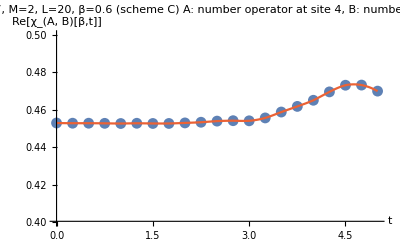

```mathematica
Show[ListPlot[Transpose[{Subscript[t, list],Re[Subscript[χ, list]]}],PlotRange->{Automatic,{0.4,0.5}},AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->Subscript[plot, label]<>"\nred: independent interpolation"],Plot[Interpolation[Transpose[{Subscript[t, list],Re[Subscript[χ, list]]}]][τ],{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"chiAB_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

```mathematica
Subscript[t, plot]=Range[0,5];
```

{{1,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,8,8,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,8,9,12,12,10,8,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,8,11,16,16,12,8,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,9,15,22,22,15,9,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,12,20,28,28,21,12,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,15,25,35,36,25,14,10,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,18,32,47,47,32,17,12,8,8,8,8,8,8,8,8,8,8,8,1},{1,9,23,44,61,60,44,22,13,8,8,8,8,8,8,8,8,8,8,8,1},{1,9,30,56,77,78,55,31,16,9,8,8,8,8,8,8,8,8,8,8,1},{1,9,39,69,97,99,69,38,21,11,8,8,8,8,8,8,8,8,9,8,1},{1,9,48,87,127,129,86,48,26,14,9,8,8,8,8,8,8,8,9,8,1},{1,9,57,111,163,166,110,60,33,15,12,8,8,8,8,8,8,8,9,8,1},{1,9,64,146,210,213,142,76,42,21,13,8,8,8,8,8,8,8,9,8,1},{1,9,68,187,266,267,183,97,51,28,15,9,8,8,8,8,8,8,9,8,1},{1,9,73,236,333,335,233,126,64,35,18,11,8,8,8,8,8,8,9,8,1},{1,9,75,287,419,422,296,163,80,44,24,14,8,8,8,8,8,8,9,8,1},{1,9,76,338,526,529,369,207,103,52,30,15,11,8,8,8,8,8,9,8,1},{1,9,77,385,660,666,462,265,133,66,37,18,13,8,8,8,8,8,9,8,1},{1,9,77,426,821,834,582,334,171,84,46,24,14,8,8,8,8,8,9,8,1},{1,9,77,460,1015,1042,735,418,217,109,54,31,15,10,8,8,8,8,9,8,1}}

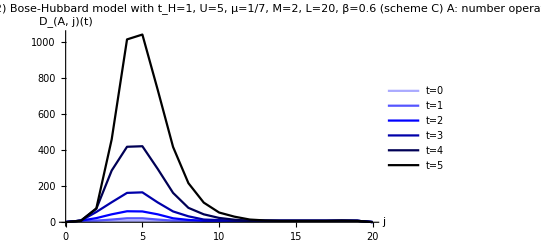

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

{{1,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,8,8,9,10,8,8,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,8,9,12,13,10,8,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,8,11,16,17,12,8,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,9,15,21,22,15,9,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,11,19,27,28,20,12,8,8,8,8,1},{1,8,8,8,8,8,8,8,8,8,14,25,35,37,25,14,10,8,8,8,1},{1,8,8,8,8,8,8,8,8,10,18,33,47,48,33,17,12,8,8,8,1},{1,8,8,8,8,8,8,8,8,12,22,43,61,61,44,22,14,8,8,8,1},{1,8,8,8,8,8,8,8,9,15,30,55,77,79,54,31,16,9,8,8,1},{1,8,8,8,8,8,8,8,12,19,39,69,97,99,70,39,20,13,9,8,1},{1,8,8,8,8,8,8,8,14,25,48,86,127,129,87,48,26,14,10,8,1},{1,8,8,8,8,8,8,10,16,33,59,110,163,166,110,60,33,15,12,8,1},{1,8,8,8,8,8,8,11,22,41,75,143,209,212,142,76,43,22,14,8,1},{1,8,8,8,8,8,9,14,28,50,96,185,265,267,184,99,51,29,15,8,1},{1,8,8,8,8,8,11,17,37,64,123,235,331,336,234,126,65,36,19,8,1},{1,8,8,8,8,8,13,22,46,82,160,296,416,422,297,163,81,44,25,9,1},{1,8,8,8,8,10,15,29,54,105,204,370,523,528,370,208,105,53,31,9,1},{1,8,8,8,8,12,18,36,66,136,260,464,659,664,462,267,136,67,37,9,1},{1,8,8,8,9,14,25,44,85,174,329,584,828,831,583,335,174,87,45,9,1},{1,8,8,8,10,15,32,54,108,220,412,736,1036,1038,736,420,219,111,52,9,1}}

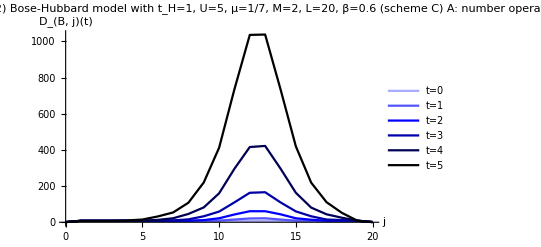

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```